## Paquetes y definiciones

```mathematica
<<QuantumWalks`
<<QMB`
```

Estas son las funciones de QuantumWalks:

```mathematica
?QuantumWalks`*
```

```mathematica
?QuantumWalks`Billiards`Generate*
```

```mathematica
?QuantumWalks`CTQW`CTQWHamiltonian
```

## Bunimovich

```mathematica
(*Construir la geometría*)
geometry=GenerateBunimovichBasis[20,20];
```

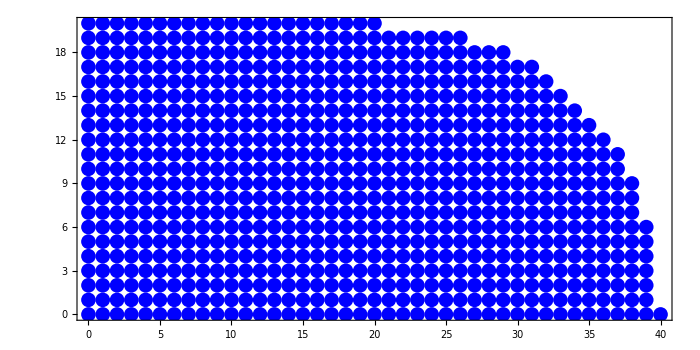

```mathematica
(*Visualize the grid*)
ListPlot[geometry["Coords"],PlotStyle->{PointSize[0.015],Blue},AspectRatio->Automatic,Frame->True,ImageSize->700,FrameStyle->Directive[Black,22]]
```

```mathematica
H=-BuildAdjacencyMatrix[geometry];
```

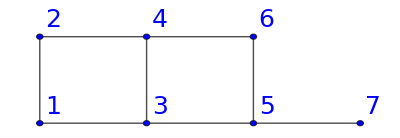

```mathematica
(*Visualizar el grafo*)
AdjacencyGraph[BuildAdjacencyMatrix[geometry],VertexCoordinates->geometry["Coords"],VertexLabels->"Name",VertexStyle->Blue,VertexLabelStyle->Directive[25],EdgeStyle->Directive[Black,Thick]]
```

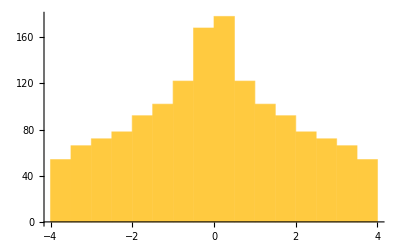

```mathematica
Histogram[Eigenvalues[Normal@H],Automatic,"Intensity"]
```

```mathematica
unfolded=Unfold[Eigenvalues[Normal@H]]["UnfoldedLevels"];
```

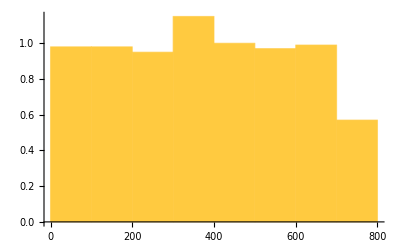

```mathematica
Histogram[unfolded,Automatic,"Intensity"]
```

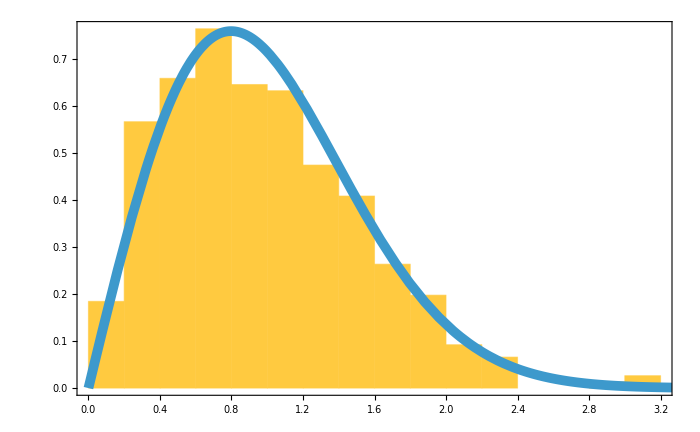

```mathematica
Show[
Histogram[Differences[unfolded],Automatic,"PDF",Frame->True,FrameStyle->Directive[Black,28],FrameLabel->{"", ""},ImageSize->700],
Plot[PDF[RayleighDistribution[Sqrt[2/Pi]],s],{s,0,4},PlotStyle->Thickness[0.01]]
]
```

```mathematica
geometry=GenerateBunimovichBasis[50,50];
```

```mathematica
H=CTQWHamiltonian[geometry]
```

SparseArray[…]

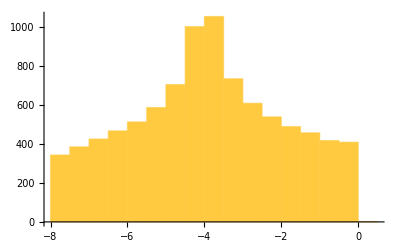

```mathematica
Histogram[Eigenvalues[Normal@H],Automatic,"Intensity"]
```

```mathematica
unfolded=Unfold[Eigenvalues[Normal@H]]["UnfoldedLevels"];
```

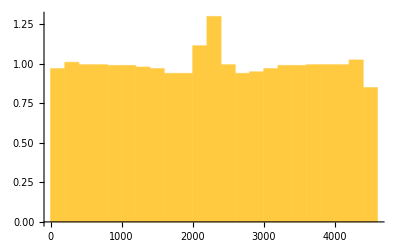

```mathematica
Histogram[unfolded,Automatic,"Intensity"]
```

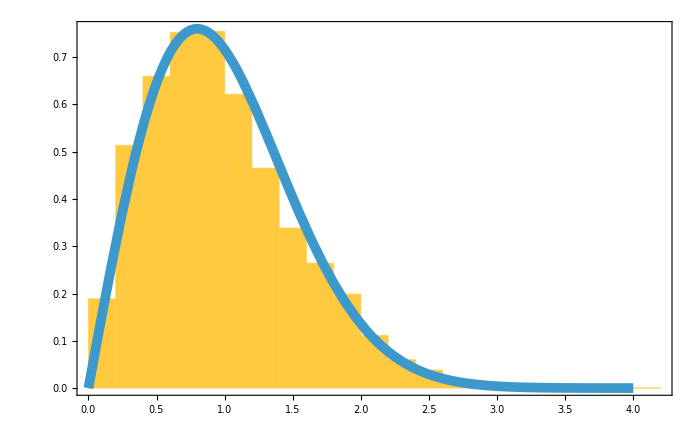

```mathematica
Show[
Histogram[Differences[unfolded],Automatic,"PDF",Frame->True,FrameStyle->Directive[Black,28],FrameLabel->{"", ""},ImageSize->700],
Plot[PDF[RayleighDistribution[Sqrt[2/Pi]],s],{s,0,4},PlotStyle->Thickness[0.01]]
]
```

```mathematica
H=CTQWHamiltonian[geometry,1.0,{{1,0},{-1,0},{0,1},{0,-1},{1,1},{-1,1},{1,-1},{-1,-1}}]
```

SparseArray[…]

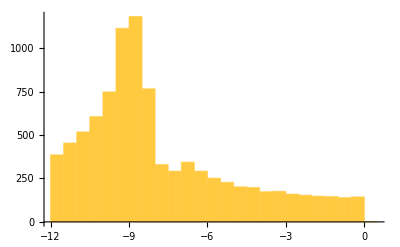

```mathematica
Histogram[Eigenvalues[Normal@H],Automatic,"Intensity"]
```

```mathematica
unfolded=Unfold[Eigenvalues[Normal@H]]["UnfoldedLevels"];
```

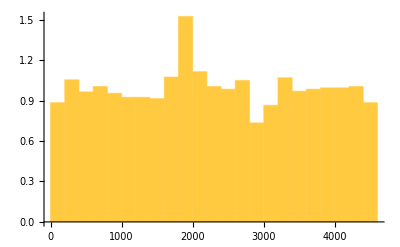

```mathematica
Histogram[unfolded,Automatic,"Intensity"]
```

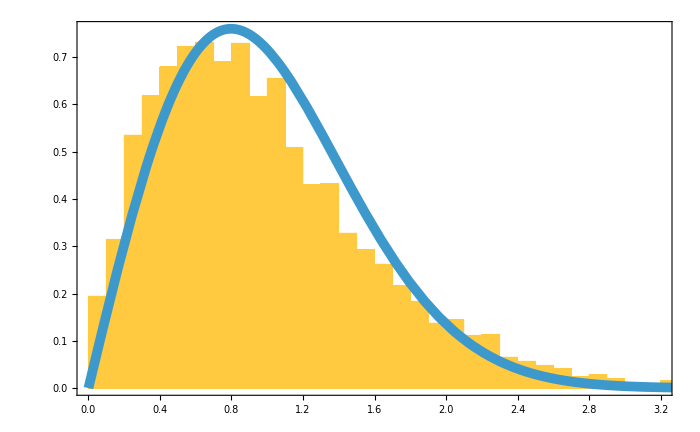

```mathematica
Show[
Histogram[Differences[unfolded],Automatic,"PDF",Frame->True,FrameStyle->Directive[Black,28],FrameLabel->{"", ""},ImageSize->700],
Plot[PDF[RayleighDistribution[Sqrt[2/Pi]],s],{s,0,4},PlotStyle->Thickness[0.01]]
]
```

## Rectangulo

```mathematica
(*Construir la geometría*)
geometry=GenerateRectangleBasis[50,25];
```

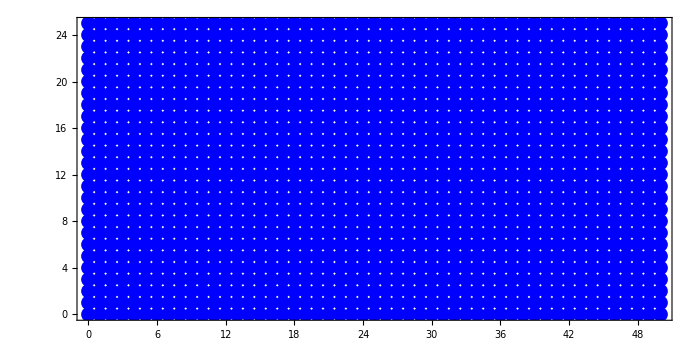

```mathematica
(*Visualize the grid*)
ListPlot[geometry["Coords"],PlotStyle->{PointSize[0.015],Blue},AspectRatio->Automatic,Frame->True,ImageSize->700,FrameStyle->Directive[Black,22]]
```

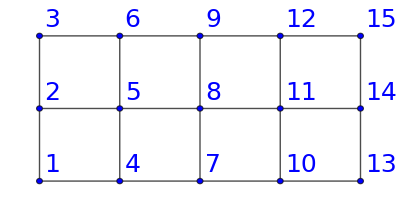

```mathematica
(*Visualizar el grafo*)
AdjacencyGraph[BuildAdjacencyMatrix[geometry],VertexCoordinates->geometry["Coords"],VertexLabels->"Name",VertexStyle->Blue,VertexLabelStyle->Directive[25],EdgeStyle->Directive[Black,Thick]]
```

```mathematica
geometry=GenerateRectangleBasis[80,40];
H=CTQWHamiltonian[geometry]
```

SparseArray[…]

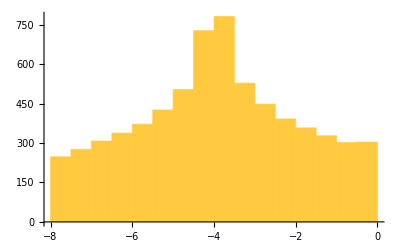

```mathematica
evals=Eigenvalues[Normal@H];
Histogram[evals,Automatic,"Intensity"]
```

```mathematica
Unfold[evals]["Bandwidth"]
```

0.355567

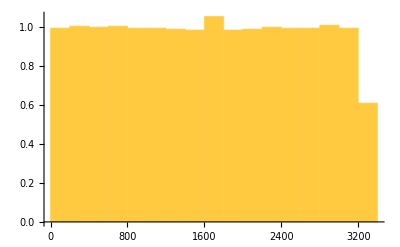

```mathematica
unfolded=Unfold[evals,"Bandwidth"->0.1]["UnfoldedLevels"];
Histogram[unfolded,Automatic,"Intensity"]
```

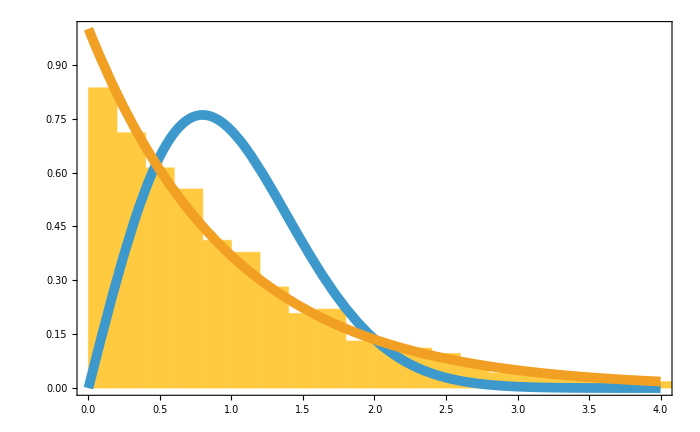

```mathematica
Show[
Histogram[Differences[unfolded],Automatic,"PDF",Frame->True,FrameStyle->Directive[Black,28],FrameLabel->{"", ""},ImageSize->700],
Plot[{PDF[RayleighDistribution[Sqrt[2/Pi]],s],Exp[-s]},{s,0,4},PlotStyle->Thickness[0.01]]
]
```

## Caridioide, Sinai, Full Bunimovich, circular? Saúl?

SFF?

P(r) de vecinos de largo alcance en billares no desimetrizados

```mathematica
?QuantumWalks`Billiards`Generate*
```